## Lesson 18: Euler equations

## Overview

In the previous lesson, you studied a differential equation with functional coefficients:

P(x)y''(x)+Q(x)y'(x)+R(x)y(x)=0

You found that there is a general series solution if the point is ordinary. That is when:

P(x_o)≠0

This lesson considers solving differential equations with singular points P(x_o)=0 and closely examines a special class of these equations known as Euler equations:

x^2 y''(x)+α x y'(x)+β y(x)=0

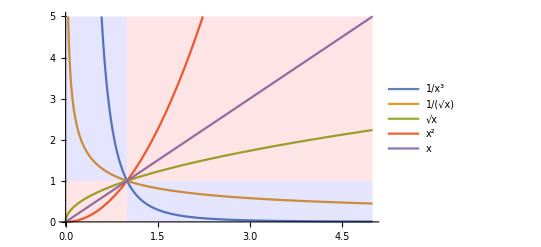

```mathematica
Show[Plot[{x^-3,x^(-1/2) ,x^(1/2),x^2 ,x},{x,0,5},],Graphics[],Graphics[],Graphics[],Graphics[]]
```

## Euler Equations

Euler equations take the form of:

x^2 y''(x)+α x y'(x)+β y(x)=0

Euler observed that by utilizing the power rule (x^r)'=(r(x))^(r-1), the differential equation could be transformed into a simpler form:

x^2(x^r)''+α x (x^r)'+β x^r=0

After some simplifications, the equation will become:

```mathematica
(x^2 y''[x]+α x y'[x]+β y[x]==0)/.y->Function[x,x^r]//Simplify
```

x^r (r^2+r (-1+α)+β)==0

Whenever r is a root to this quadratic equation, then x^r will be a solution to the differential equation.

How will solutions change for different classes of roots: real unique roots, repeated roots and complex roots?

## Euler Equations: Distinct Roots

If the quadratic polynomial from the previous slide has distinct roots r_1 and r_2:

x^r(r(r-1)+α r+β)=0

then there are two solutions: x^r_1 and x^r_2.

Examining the Wronskian:

```mathematica
Wronskian[{x^Subscript[r, 1],x^Subscript[r, 2]},x]
```

x^(-1+r_1+r_2) (-r_1+r_2)

you can see that because r_1≠r_2, the Wronskian is nonzero for x>0.

It follows that you have formed a fundamental solution set and the general solution is:

y=c_1 x^r_1+c_2 x^r_2          x>0

## Example 1

Solve the equation:

x^2 y''(x)+6 x y'(x)+6 y(x)=0

Substitute y(x) = x^r:

```mathematica
(x^2 y''[x]+6 x y'[x]+6 y[x]==0)/.y->Function[x,x^r]//Simplify
```

(6+5 r+r^2) x^r==0

Thus whenever (6+5 r+r^2)=0, x^r solves the differential equation:

```mathematica
Roots[6+5r+r^2==0,r]
```

r==-3||r==-2

Thus two solutions to the differential equation are x^-3 and x^-2.

You can check this with DSolveValue:

```mathematica
DSolveValue[x^2 y''[x]+6x y'[x]+6y[x]==0,y[x],x]
```

C[1]/x^3+C[2]/x^2

## Euler Equations: Repeated Roots

When the roots are repeated, there is only one solution: x^r.

If you can recall from the lesson on second-order equations with constant coefficients, it used a method originated by d’Alembert where you assume the function takes the form:

y(x)=u(x)x^r_1

Through this method, you can find that the second solution for repeated roots is x^r_1 ln(x).

Examining the Wronskian:

```mathematica
Wronskian[{x^Subscript[r, 1],Log[x] x^Subscript[r, 1]},x]
```

x^(-1+2 r_1)

you see that the Wronskian is nonzero for x>0.

It follows that you have formed a fundamental solution set and the general solution is:

y(x)=c_1 x^r_1+c_2 ln(x)x^r_1          x>0

## Example 2

Solve the equation:

x^2 y''(x)+7 x y'(x)+9y(x)=0

Substitute y(x)=x^r:

```mathematica
(x^2 y''[x]+7 x y'[x]+9 y[x]==0)/.y->Function[x,x^r]//Simplify
```

(3+r) x^r==0

There is only one root to the equation, which is r=-3.

Thus two solutions to the differential equation are x^-3 and ln(x)x^-3.

You can check this with DSolveValue:

```mathematica
DSolveValue[x^2 y''[x]+7 x y'[x]+9 y[x]==0,y[x],x]
```

C[1]/x^3+(3 C[2] Log[x])/x^3

## Euler Equations: Complex Roots

In the case for complex roots, the solutions take the form x^(a±ⅈ b).

Using the properties of logarithms and exponential functions combined with Euler’s formula, this expression can be transformed:

```mathematica
x^(a+I b)==x^a(Cos[b Log[x]]+I Sin[b Log[x]])//FullSimplify
```

True

Now you have found two solutions to the differential equation, namely:

x^a cos(b ln(x))

x^a sin(b ln(x))

Examining the Wronskian:

```mathematica
Wronskian[{x^a Cos[b Log[x]],x^a Sin[b Log[x]]},x]
```

b x^(-1+2 a)

you see that the Wronskian is nonzero for x>0 and b≠0. You know b is not zero or else the root would not be complex.

It follows that you have formed a fundamental solution set and the general solution is:

y=c_1 x^a cos(b ln(x))+c_2 x^a sin(b ln(x))          x>0

## Example 3

Solve the equation:

x^2 y''(x)+5 x y'(x)+6 y=0

Substitute y(x) = x^r:

```mathematica
(x^2 y''[x]+5 x y'[x]+6 y[x]==0)/.y->Function[x,x^r]//Simplify
```

(6+4 r+r^2) x^r==0

Thus whenever (6+4 r+r^2)=0, x^r solves the differential equation:

```mathematica
Roots[6+4r+r^2==0,r]
```

r==-2-ⅈ √2||r==-2+ⅈ √2

Thus two solutions to the differential equation are:

x^-2 cos(√2 ln(x))

x^-2 sin(√2 ln(x))

You can check this with DSolveValue:

```mathematica
DSolveValue[x^2 y''[x]+5 x y'[x]+6 y[x]==0,y[x],x]
```

(C[2] Cos[√2 Log[x]])/x^2+(C[1] Sin[√2 Log[x]])/x^2

## Qualitative Behavior

All of the solutions are largely dependent on the functions x^a:

c_1 x^r_1+c_2 x^r_2

c_1 x^r_1+c_2 ln(x)x^r_1

c_1 x^a cos(b ln(x))+c_2 x^a sin(b ln(x))

Recall the qualitative behavior of the power functions for different values of a:

```mathematica
Show[Plot[{x^-3,x^(-1/2) ,x^(1/2),x^2 ,x},{x,0,5},],Graphics[],Graphics[],Graphics[],Graphics[]]
```

-Graphics-

You can see quite clearly that solutions with negative roots approach ∞ as x→0.

## Qualitative Behavior: Distinct Real Roots

Solutions with real roots have the form:

c_1 x^r_1+c_2 x^r_2

Thus solutions are stable only when both roots are negative.

If either r_1 or r_2 is positive, the solution will diverge to positive or negative infinity.

This result agrees with the solution in Example 1:

```mathematica
DSolveValue[x^2 y''[x]+6x y'[x]+6y[x]==0,y[x],x]
```

C[1]/x^3+C[2]/x^2

Use Limit to show that this functions converges to zero for any values of c_1 and c_2:

```mathematica
Limit[C[1]/x^3+C[2]/x^2,x->∞]
```

0

## Qualitative Behavior: Repeated Roots

Solutions with repeated roots have the form:

c_1 x^r_1+c_2 ln(x)x^r_1          x>0

Thus solutions are stable only when the real root is negative so that x ln(x)<x^a for large enough x:

```mathematica
Limit[x^a Log[x] ,x-> ∞,Assumptions->a<0]
```

0

The solution in Example 2 satisfies this property with a=-3:

```mathematica
DSolveValue[x^2 y''[x]+7x y'[x]+9y[x]==0,y[x],x]
```

C[1]/x^3+(3 C[2] Log[x])/x^3

A Plot of the solution follows for values of c_1=c_2=1:

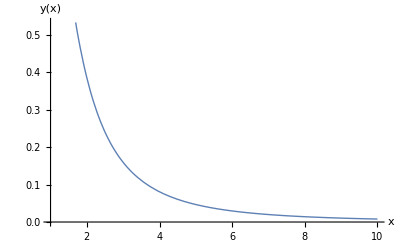

```mathematica
Plot[1/x^3+(3 Log[x])/x^3,{x,1,10},]
```

## Qualitative Behavior: Complex Roots

Solutions with complex roots have the form:

c_1 x^a cos(b ln(x))+c_2 x^a sin(b ln(x))

The qualitative behavior is again largely determined by the value of a in the function x^a.

The solution in Example 2 satisfies this property with a=-2:

```mathematica
DSolveValue[x^2 y''[x]+5x y'[x]+6y[x]==0,y[x],x]
```

(C[2] Cos[√2 Log[x]])/x^2+(C[1] Sin[√2 Log[x]])/x^2

This plot displays one solution with c_1=c_2=1:

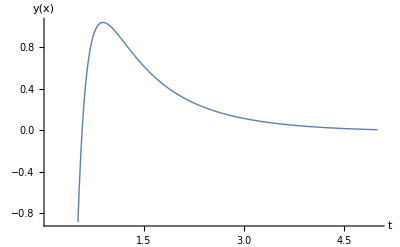

```mathematica
Plot[Cos[√2 Log[x]]/x^2+Sin[√2 Log[x]]/x^2,{x,.1,5},]
```

## Summary

This lesson examined the solution methods for a particular class of second-order differential equations known as Euler equations.

These are equations that take the form:

x^2 y''(x)+α x y'(x)+β y(x)=0

You were able to determine the solutions for any constants α and β.

These solutions take on three different forms:

c_1 x^r_1+c_2 x^r_2

c_1 x^r_1+c_2 ln(x)x^r_1

c_1 x^a cos(b ln(x))+c_2 x^a sin(b ln(x))

In the next lesson, you will find out how the Euler equation plays a critical role in finding solutions near a singular point.